# Project 9: Regression via Optimization

## Note: Perhaps this should be called parameter estimation via optimization.

Consider the following data.

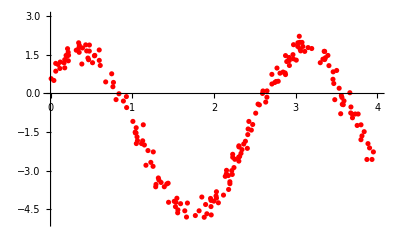

```mathematica
numPoints=200;
X=RandomVariate[UniformDistribution[{0,4}],numPoints];
error=RandomVariate[NormalDistribution[0,0.3],numPoints];
g[s_]:=3.15*Sin[2.3*s+0.7]-1.5;
Y=g[X]+error;
data=Transpose[{X,Y}];
ListPlot[data,PlotStyle->Red,PlotRange->{{0,4},{-5,3}}]
```

The aim of this project is to use the Steepest Descent algorithm acting on the “spring potential energy” function associated to the data above, and the family of functions given by

```mathematica
h[s]:=a*Sin[b*s+c]+d;
```

where a, b, c, and d are unknown constants, which become the arguments of the “spring potential energy” function.  You can (and should) copy and edit code from class to achieve this.  Add this code below, and export this notebook to a pdf and submit it to GradeScope.  Your completed work should contain a working Steepest Descent algorithm which starts at the function h(s)=0.5 sin(x); that is, corresponding to a=0.5, b=c=d=0.  Additionally, you must plot the optimizing function your code obtains, overlayed on the above data, to show that it is a good fit.

{-0.00577855 Sin[0.00734171 b+c]+1/100 d Sin[0.00734171 b+c]+1/100 a Sin[0.00734171 b+c]^2-0.00508185 Sin[0.0410074 b+c]+1/100 d Sin[0.0410074 b+c]+675+1/100 d Sin[3.93305 b+c]+1/100 a Sin[3.93305 b+c]^2+0.0227446 Sin[3.95016 b+c]+1/100 d Sin[3.95016 b+c]+1/100 a Sin[3.95016 b+c]^2,2,1.6923+2 d+198+1+1/100 a Sin[19 b+c]}
 |  |  |  |

{{3.06066,2.28449,0.743367,-1.46211},0.085844}

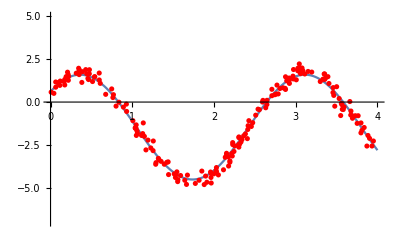

```mathematica
model[a_,b_,c_,d_,s_]:=a*Sin[b*s+c]+d;
F[a_,b_,c_,d_]:=Module[{},y[z_]:=model[a,b,c,d,z];
Total[(Y-y[X])^2]/numPoints]
dF[a_,b_,c_,d_]={D[Expand[F[a,b,c,d]],a],D[Expand[F[a,b,c,d]],b],D[Expand[F[a,b,c,d]],c],D[Expand[F[a,b,c,d]],d]}

maxGradAllowed=1.0;
x={2,2,2.5,-1};
h=0.1;
threshold=0.1;
grad=Apply[dF,x];

While[Sqrt[grad.grad]>threshold,If[Sqrt[grad.grad]>maxGradAllowed,grad=maxGradAllowed*grad/Sqrt[grad.grad]];
xNew=x-h*grad;
If[Apply[F,xNew]<Apply[F,x],x=xNew,h=h/10];
grad=Apply[dF,x];]
Print[{x,Apply[F,x]}];

f[s_]:=(x[[1]])*Sin[x[[2]]*s+(x[[3]])]+(x[[4]]);
A=ListPlot[data,PlotStyle->Red,PlotRange->{{0,4},{-7,5}}];
B=Plot[f[s],{s,0,4},PlotRange->{{0,4},{-7,5}}];
Show[B,A]
```